# Parser

Parser for the grammar:

## Recursive descent parser

```mathematica
MapUntil[f_,expr_,test_]:=Drop[
NestWhileList[
{f[#[[2,1]]],Drop[#[[2]],1],(!test[f[#[[2,1]]]]&& Length[#[[2]]]≠1)}&,
{0,expr,True},
#[[3]]&
][[All,1]],
1];
```

```mathematica
MapUntil[f,Range[5],#=!=$Failed&]
```

{$Failed,2}

```mathematica
MapUntil[f,Range[5],#===7&]
```

{$Failed,2,3,4,5}

```mathematica
Protect[EmptyString,Term,NonTerm];

GetArgument[_[arg_]]:=arg;
Match[input_,terms_]:=(Take[input,Length[terms]] == Map[GetArgument,terms]);
GenerateTransition[rule_,stateId_,lastId_]:=MapIndexed[{rule["From"],stateId}->{#1,lastId+First[#2]}&,rule["To"]];

MatchTerminalsWithRule[stateId_,lastId_,input_,rule_]:=Block[{terms,transition,rest,cuttedInput,currentState,lastIndex},

currentState = rule["From"];
If[rule["To"]===EmptyString,Return[{{{currentState,stateId}->{EmptyString,lastId+1}},{},input,lastId+1}]];

transition = GenerateTransition[rule,stateId,lastId];
lastIndex = Last@Last@Last@transition;
terms = TakeWhile[rule["To"],Head[#]=!=NonTerm&];
rest = Drop[transition[[All,2]],Length[terms]];

If[Length[terms]>Length[input],Return[$Failed]];

If[Match[input,terms],
cuttedInput = Drop[input,Length[terms]];
Return[{transition,rest,cuttedInput,lastIndex}];
,
Return[$Failed];
];
];

MatchTerminals[{state_,stateId_},lastId_,input_,grammar_]:=Block[{possibleTransitions,matched},
possibleTransitions = Cases[grammar,KeyValuePattern[{"From"->state}]];
matched = Last[MapUntil[MatchTerminalsWithRule[stateId,lastId,input,#]&,possibleTransitions,#=!=$Failed&]];
Return[matched];
];
```

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
MatchTerminals[{NonTerm["E"],1},4,{"i","+","i","$"},grammar]
```

{{{NonTerm[E],1}→{NonTerm[T],5},{NonTerm[E],1}→{NonTerm[E'],6}},{{NonTerm[T],5},{NonTerm[E'],6}},{i,+,i,$},7}

Parser

```mathematica
Parse[input_,grammar_]:=Block[{stack,transitions,next,inputBuffer,lastId,parseTree,parseSymbol,toStack},
stack = {};
parseTree = {};
lastId = 1;
inputBuffer = Characters[StringJoin[input,"$"]];
parseSymbol = {First[grammar]["From"],1};

While[{inputBuffer,parseSymbol} =!= {{"$"},None},
If[Head[First[parseSymbol]] ===NonTerm,
{transitions,next,inputBuffer,lastId} = MatchTerminals[parseSymbol,lastId,inputBuffer,grammar];
,
If[GetArgument[First[parseSymbol]] == First[inputBuffer],
inputBuffer =Drop[inputBuffer,1];
next = {};
];
];

If[Length[next]>0,
(* Push *)
AppendTo[parseTree,transitions];
{parseSymbol,toStack}={First[next],Rest[next]};
stack = Join[stack,toStack];
,
(* Pop *)
If[Length[stack] > 0,
{parseSymbol,stack}={Last[stack],Drop[stack,-1]};
,
parseSymbol = None;
];
];
];

Return[Flatten[parseTree,1]];
];

ParseTree[input_,grammar_]:=Block[{parseTree,startProduction},
parseTree = Parse[input,grammar];
startProduction = First[First[parseTree]];

TreePlot[parseTree,Automatic,startProduction,VertexLabeling->True]
];
```

Grammar 1

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{Term["i"],NonTerm["E'"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->{Term["j"],NonTerm["V"]}|>,
<|"From"->NonTerm["V"],"To"->EmptyString|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],Term["i"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>
};
```

```mathematica
Parse["i+i+ijj",grammar]
```

{{NonTerm[E],1}→{Term[i],2},{NonTerm[E],1}→{NonTerm[E'],3},{NonTerm[E],1}→{NonTerm[V],4},{NonTerm[E'],3}→{Term[+],5},{NonTerm[E'],3}→{Term[i],6},{NonTerm[E'],3}→{NonTerm[E'],7},{NonTerm[E'],7}→{Term[+],8},{NonTerm[E'],7}→{Term[i],9},{NonTerm[E'],7}→{NonTerm[E'],10},{NonTerm[V],4}→{Term[j],12},{NonTerm[V],4}→{NonTerm[V],13},{NonTerm[V],13}→{Term[j],14},{NonTerm[V],13}→{NonTerm[V],15}}

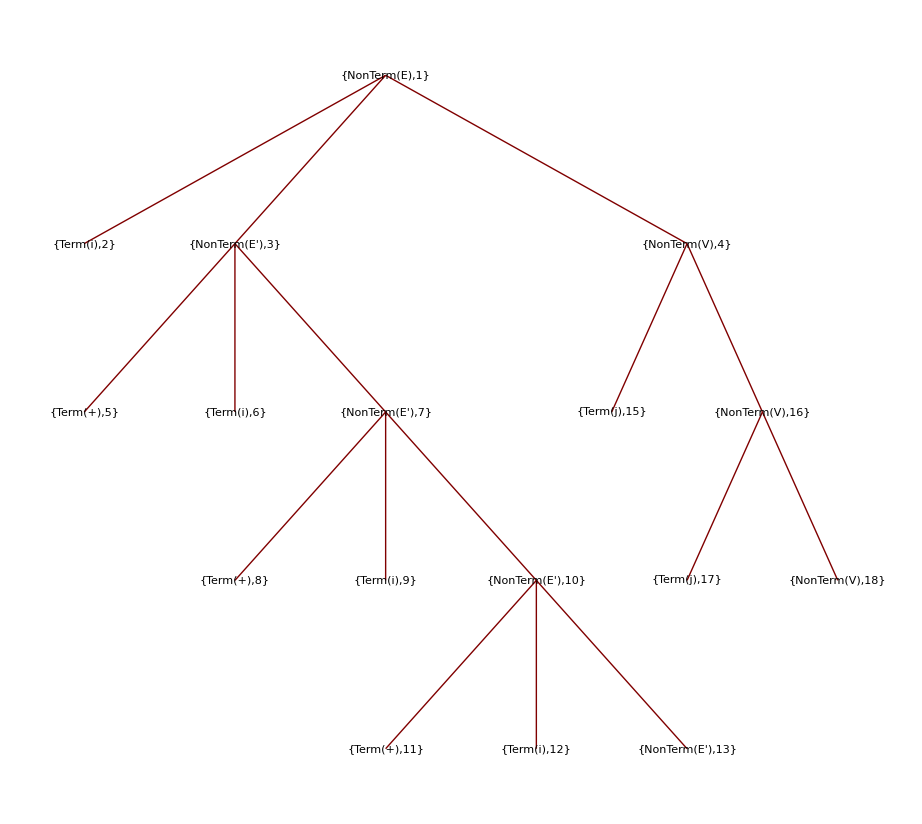

```mathematica
ParseTree["i+i+i+ijj",grammar]
```

```mathematica
.b4
```

Grammar 2

```mathematica
grammar = {
<|"From"->NonTerm["E"],"To"->{NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->{Term["+"],NonTerm["T"],NonTerm["E'"]}|>,
<|"From"->NonTerm["E'"],"To"->EmptyString|>,

<|"From"->NonTerm["T"],"To"->{NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->{Term["*"],NonTerm["F"],NonTerm["T'"]}|>,
<|"From"->NonTerm["T'"],"To"->EmptyString|>,

<|"From"->NonTerm["F"],"To"->{Term["i"]}|>,
<|"From"->NonTerm["F"],"To"->{Term["("],NonTerm["E"],Term[")"]}|>
};
```

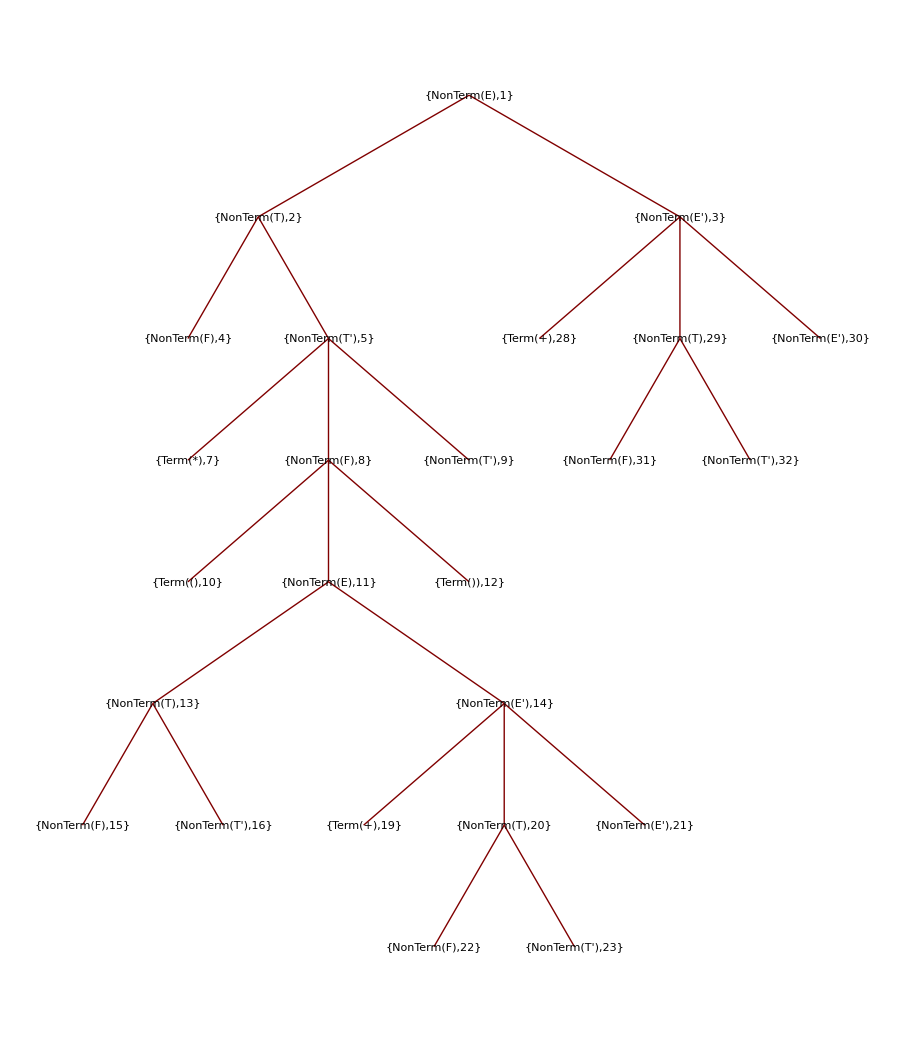

```mathematica
ParseTree["i*(i+i)+i",grammar]
```